# 医学生物学分野における引用グラフの成長

## 要旨

PubMedの3000万件を超える収録記事を対象として、レファレンス情報を抽出し、レファレンスネットワークの構造変化を75年間にわたり俯瞰する。

## 背景

大規模な引用関係の分析は、雑誌間あるいは組織間等のある程度まとまったレベルでの関係に注目されることが多かった。これは、論文を要素とする大規模な引用関係をそのまま分析するには粒度が小さすぎるためである。あるいは、この問題の回避には、論文をクラスタリングする方法があり、引用関係や研究テーマでの分類が可能であるが、明確な粒度の線引きは簡単ではない。それでも、妥当な粒度を見つけ出し分析した研究は多い。Leydesdorff[1,2,3,4]は雑誌間の関係マップを構築・調査した。天野ら[5,6]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにしている。近年ではLiら[7]が長期にわたる引用の特徴を、2300万論文をグループ化して調査した。しかしながら、これらはどちらかと言えば短期間の分析である。いままで、長期に渡り論文レベルの引用ネットワーク構造そのものが、どのように変化するのかは確認されていない。そこで本研究では、論文単位のレファレンスネットワークそのものを直接分析する。また、長期的な変化を捉えるために、75年間のレファレンス情報を利用する。この際、前述の粒度問題に対しては明確な構造的な分離による単位、すなわちWeakly-connected component graphを単位とすることで対応し、Weakly-connected component graph の結合構造の変化を明らかにする。

## 目的

論文単位の引用ネットワークが、長期的にどのように変化するのかを、さまざまなネットワーク指標を用いて観察する。

## マテリアル

### データ

FTP版のPubmed baseline (2023)[8]を利用する。レファレンスネットワークの構成は、ubMedに収録されている論文のうち出版年が1946-2020のものに記載されるレファレンスを対象とし、次に述べる方法で「世代」を構築する。

本研究で用いた2023年のFTP版PubMed annual baselineの概要を表1に示す。わずかに2024年の論文も含まれている。

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

表 2

PubMed annual baselineのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

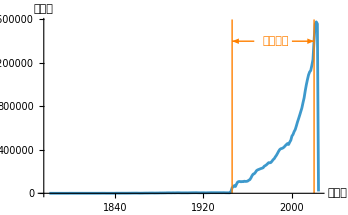

図1

PubMed annual baselineの登録論文数の推移

### 世代の構成

本研究ではレファレンスネットワーク全体がどのように成長するかを見るため、世代を累積的に構成する。これを「累積世代」と称する。まず、1946-2020年の出版論文をオーバーラップなしの5年ごとの出版に分け、これらの論文集合のレファレンス情報から、15層のレファレンスネットワークを構成した。次に、第一層から累積的に一層ずつ層を結合し、第15累積世代では1~15層が結合されたレファレンスネットワークとなるようにネットワークの累積世代を構成した。対象となる記事のタイプは全てである。また、この構成では1946年より前に出版された論文も対象に含まれる。

### Weakly-connected component graph

本研究ではレファレンスネットワーク構造の変化を計量的に観察する。このため、ネットワーク全体をより下位のネットワークに分け、その変化を観察する。レファレンスネットワーク全体の下位構造として想定されるものには、引用関係、共著関係によるネットワークの分割や、テーマによる分類等がある。本研究ではネットワークを最も直接的かつ明確に分ける単位として引用による弱連結グラフ（Weakly-connected component graph: WCC）を採用する。前述の方法にて累積世代グラフを構築したのち、WCCのサイズや個数、前世代のWCCと当該世代のWCCを繋ぐリンク等に注目し分析する。

## 結果

### 累積世代ごとのレファレンスネットワーク構造の変化

累積世代ごとのレファレンスネットワーク全体に関してのエッジ総数と複雑度を図1に示す。複雑度については、ノード間の距離に無限大が存在しても発散しないサイクロマティック複雑度(<エッジ数> - <ノード数> + 2 <コンポーネント数>)[9]を用いた。加えて、累積世代ごとのWCCのノード総数、最大WCCのノード数、WCC数および孤立ノード数を、同じく図1に示す。これらはすべて増加傾向にある。なお、WCCノード総数の70%以上を最大WCCのノードが占めている。

また、以上の属性の増加率（微分）を図2に示す。これによれば、全ネットワークにおけるエッジ総数と複雑度は加速度的な上昇を見せている。WCCノード総数と最大WCCノード数も同じく加速度的な増加を見せている。WCC数の増加率については増減があるものの、その変化は一定の幅の内に見られる。孤立ノード数は上昇傾向ではあるものの、増加率については1946-1995年累積世代以降低くなってきている。

次に、総WCCノードにおける最大WCCノード数の占有率、ネットワークの総ノードにおける最大WCCノード数の占有率およびネットワークの総ノードにおける孤立ノードの占有率を図3に示す。これによれば最大WCCはその占有率を増加させ続けており、孤立ノードの占有率は減少傾向にある。

-Graphics-

図1 全ネットワークおよびWCCに関する基本的な統計値

-Graphics-

図2 全ネットワークおよびWCCに関する基本的な統計値の増加率

-Graphics-

図3 各種ノードの占有率

### レファレンスネットワークの成長要素

検討事項：WCCを統合するリンク（論文）の特性を研究テーマで見る。
(0)累積世代内のテーマ
(1)累積世代間のリンクテーマの推移 -> リンク論文を抽出しているか確認する
(2)WCC間のリンクテーマの差異（上位25パーセンタイルのWCC）

ここでは累積世代間のネットワークの差分を見ることにより、レファレンスネットワークの成長を捉える。成長をノードの発生、エッジの発生、これらによるネットワーク全体の構造変化ととらえ、構造変化に関してはWCGの結合に注目する。ノードの発生については新規出版と同義であるため特に言及しない。以下ではエッジの発生とWCGの結合に関する次の項目を調査する。

新規に発生した引用数

新規に発生した引用により結合が発生した前世代WCG数

新規に発生した引用に関して異なる前世代WCGを結合(引用)する論文の数

新規に発生した引用により異なる前世代WCGと結合された前世代WCG数

また、以上とは別にWCGの結合における主要論文の寄与を調べる。

##### 6.2.1 世代間で新たに発生した引用関係とこれにより結合されるWCG

6.2に挙げた項目の調査結果を表9に示す。新規に発生する引用やWCGの結合に寄与する論文は出版される論文の増加にともない増加する傾向にある。一方、他のWCGと結合されるWCGの割合は幅があるものの一定の傾向を見せている。

表9

累積世代間のレファレンスネットワークの差分に関する属性

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
主要論文に対する引用数(%) | 新規に発生した引用に関して
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数 | 前世代WCG数 | WCGの結合率
1955 | 148555 | 718 (0.5) | 1632 | 1280 | 909 | 2353 | 0.39
1960 | 291655 | 3109 (1.1) | 1942 | 1485 | 1185 | 3851 | 0.31
1965 | 445022 | 8846 (2.) | 1717 | 1297 | 1070 | 4624 | 0.23
1970 | 818629 | 26986 (3.3) | 1937 | 1411 | 1133 | 5729 | 0.2
1975 | 1369688 | 43178 (3.2) | 2240 | 1549 | 1306 | 7020 | 0.19
1980 | 1998678 | 54563 (2.7) | 2520 | 1716 | 1500 | 8446 | 0.18
1985 | 2821649 | 103101 (3.7) | 2480 | 1683 | 1478 | 9401 | 0.16
1990 | 4022714 | 230540 (5.7) | 2438 | 1553 | 1392 | 10026 | 0.14
1995 | 5715688 | 221170 (3.9) | 2345 | 1450 | 1310 | 10687 | 0.12
2000 | 6095490 | 153837 (2.5) | 1603 | 1147 | 1048 | 11361 | 0.09
2005 | 9616785 | 103356 (1.1) | 2553 | 1508 | 1353 | 12147 | 0.11
2010 | 27854672 | 221562 (0.8) | 6243 | 2576 | 2407 | 13000 | 0.19
2015 | 63696093 | 1530822 (2.4) | 11124 | 3404 | 3235 | 13398 | 0.24
2020 | 98878679 | 5603859 (5.7) | 11676 | 3472 | 3255 | 13643 | 0.24

## 考察・まとめ

## 参考

Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

Li

https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)

McCabe, T. J. (1976). A Complexity Measure. IEEE Transactions on Software Engineering, SE-2(4), 308–320.

## 検討

ノード数（N）☑️

エッジ数（M）☑️

グラフ直径（最大次数）-> メモリーオーバーにより計算不可

平均次数: M / N

密度: M / (N * (N-1))

グラフ複雑性☑️

増加率のplot

## プログラム

複雑性定義の案

graphRedundancyComplexity[g_Graph] := Module[{vc, ec, ecmean, etp},
  vc = VertexCount[g] // N;
  ec = EdgeCount[g] // N;
  ecmean = ec/(vc^2);
  etp = Entropy[AdjacencyMatrix[g] // Flatten] // N;
  (vc) (vc^ecmean) Exp[etp]
  ]